# Takeaways From our Recent Efforts in Biology: Some General Rules of Medicine

### A New Paradigm

What is the nature of biological processes? How do they look? What can they achieve? What happens when they go wrong?  These are such simple questions, and yet the field of theoretical biology, in my experience, has largely failed to give people good answers.

Part of the reason for this, I believe, is that most biologists have largely missed a powerful new class of models: those based on simple computational rules. And because of this, they have been limited in their ability to give a good high-level description of what is going on in biology. In the past year or so, Stephen Wolfram has filled this gap and pioneered some groundbreaking computational models for biological systems. Starting as a fan of the research, and eventually becoming a collaborator, I’ve become convinced that we’ve struck gold and are now in a position to understand the high-level features of biology better than ever before.

Wolfram has written three in-depth articles on this subject, the first two exploring these computational models from the perspective of evolution and biology, and the last one, which is the one that I helped him with, looking at the models from the point of view of medicine.

In all three articles, he has stayed very high-level. My aim here is to connect the high-level phenomena that he’s shown, to specific systems within biology

In particular, there is a vague assumption among some biologists, that every structure has a function, and that every mechanism within an organism can be explained. What we find in our models, is that this is not true, and that in many cases the mechanisms that adaptive systems find to achieve their goals are full of irreducibility.

And in fact, looking, for example, at the virus genome, we see that the ways in which different genes influence the shape of a particular protein, is similarly full of irreducibility.

So, what are our models and what claims can we make from them?

To model an “organism” we use what’s called a cellular automaton. In a cellular automaton, there are discrete “cells” (not to be confused with biological cells), that can be any number of discrete values, in our case either white, red, purple or yellow.  We then have a list of rules that determine how we update the values of the cells. This automaton that we’re going to use is said to be 1-dimensional, so at a given row of cells, we apply the rules that appear in that row (the top three boxes) to get the values (the bottom box) for the next row of cells. We repeat this process downward, in this case for two-hundred steps.  The rules are shown here on the right, and the result of running those rules, starting from a single red cell, is shown on the left.

```mathematica
reg[[181, 1]]
```

{109119604060725664814308901024268869132,4,1}

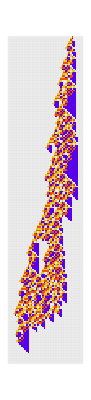
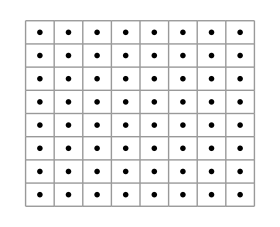

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{109119604060725664814308901024268869132,4,1},{{1},0},200],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]],RulePlot[CellularAutomaton[{109119604060725664814308901024268869132,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

But this isn’t just a random cellular automaton. We found this pattern through an “evolution”, where we start from the null ruleset (all zeroes) and repeatedly make random, single-bit changes, or “mutations”, to that ruleset. We then keep the changes that lead to a longer or equal finite length pattern. Here we show changes to the ruleset that we kept:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+181];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

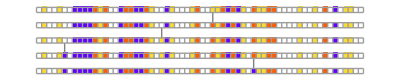
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[1;;5,1]],"Arrows"->"Line",ImageSize->400],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[100;;104,1]],"Arrows"->"Line",ImageSize->400],"⋮"},Center]
```

And here we show the steps of the evolution where a longer pattern was found. Note that we define the length of the pattern to be the number of steps before it “dies out” and reaches all-white state.

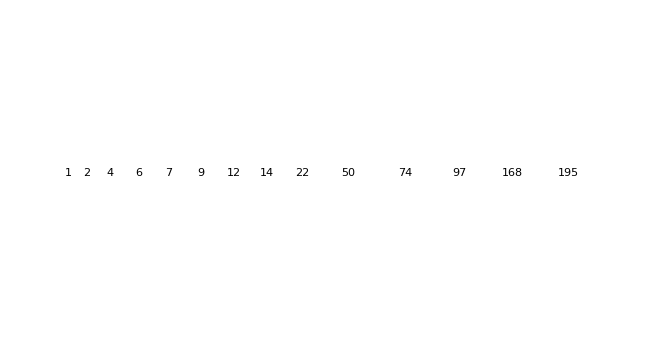

```mathematica
GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]]]
```

So we can think of the rules of the automata as the “genotype”, the resulting pattern as the “phenotype”, and the length of that pattern as the “fitness”. And in our evolution, we make random changes to the genotype (mutations), then, much like in real evolution, we keep only the changes that result in a “fitter phenotype”.

Running this process a few more times, we can get a sense for the “different paths of evolution” in our model:

```mathematica
evos = 
Table[Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+i];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
], {i,{41, 43, 105}}] ;
```

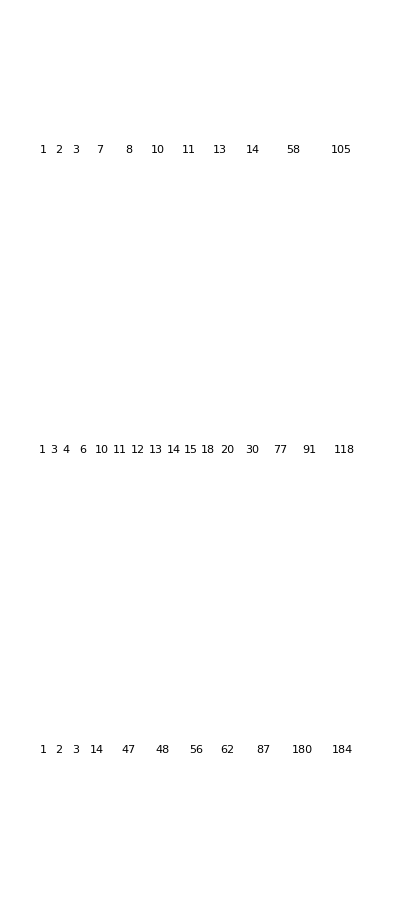

```mathematica
Column[MapThread[Function[{evo, steps}, GraphicsRow[Labeled[{{"[◼]", "PlotCA"}}[First[#],"Trim"->{1,5},ImageSize->{Automatic,22.5 Sqrt[1+Last[#]]}],Text[Style[Last[#],Small]]]&/@(Rest[evo[[ResourceFunction["ProgressiveMaxPositions"][evo[[All, -1]]]]]])]], {evos, {105, 120, 190}}],Spacer[1]]
```

And the great strength of this model,

### So what

The